# Coronavirus

## Using data from Wolfram Data Repository

Source: https://datarepository.wolframcloud.com/resources/Novel-Coronavirus

Get the data from the repository:

```mathematica
data=ResourceData["Epidemic data for novel coronavirus 2019-nCoV from Wuhan, China"];
```

Sample the data:

```mathematica
RandomSample[%,3]
```

Make a country choropleth map for the data:

```mathematica
GeoRegionValuePlot[Normal@data[GroupBy["Country"],Total,#ConfirmedCases["LastValue"]&]]
```

-Graphics-

```mathematica
cases=data[Select[MemberQ[{Entity["AdministrativeDivision",{"Hubei","China"}],Entity["AdministrativeDivision",{"Zhejiang","China"}],Entity["AdministrativeDivision",{"Guangdong","China"}]},#AdministrativeDivision]&]][All,{"AdministrativeDivision","ConfirmedCases"}];
```

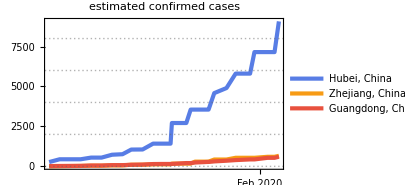

```mathematica
DateListPlot[Legended[#[[2]],#[[1]]]&/@cases,PlotTheme->"Business",PlotLabel->"estimated confirmed cases",ImageSize->300,PlotRange->Full]
```

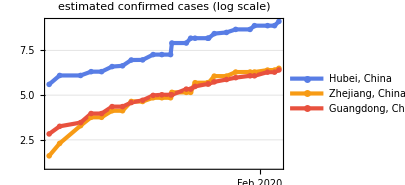

```mathematica
DateListLogPlot[Legended[#[[2]],#[[1]]]&/@cases,PlotTheme->"Business",PlotLabel->"estimated confirmed cases (log scale)",ImageSize->300,PlotRange->Full]
```